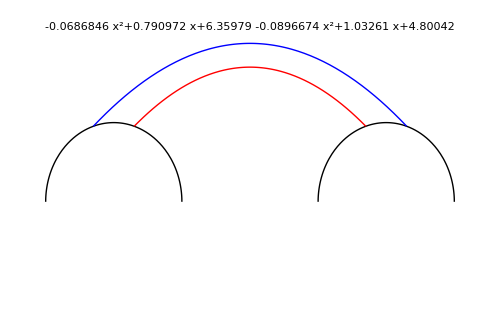

```mathematica
Module[{r,a,circle1,circle2,x1,y1,sol1,a1,b1,c1,f1,x2,y2,sol2,a2,b2,c2,f2},
r=2.879;a=4*r;
circle1[x_]=√(r^2-x^2)+r;
circle2[x_]=√(r^2-x^2-a^2+2*x*a)+r;

x1[1]=-0.3*r;y1[1]=circle1[x1[1]];
x1[2]=a/2;y1[2]=3*r;
x1[3]=a+0.3*r;y1[3]=circle2[x1[3]];

sol1=Quiet@Solve[{
α*x1[1]^2+β*x1[1]+χ==y1[1],
α*x1[2]^2+β*x1[2]+χ==y1[2],
α*x1[3]^2+β*x1[3]+χ==y1[3]
},{α,β,χ}][[1]];
a1=α/.sol1;b1=β/.sol1;c1=χ/.sol1;
f1[x_]:=a1*x^2+b1*x+c1;

x2[1]=0.3*r;y2[1]=circle1[x2[1]];
x2[2]=a/2;y2[2]=2.7*r;
x2[3]=a-0.3*r;y2[3]=circle2[x2[3]];

sol2=Quiet@Solve[{
α*x2[1]^2+β*x2[1]+χ==y2[1],
α*x2[2]^2+β*x2[2]+χ==y2[2],
α*x2[3]^2+β*x2[3]+χ==y2[3]
},{α,β,χ}][[1]];
a2=α/.sol2;b2=β/.sol2;c2=χ/.sol2;
f2[x_]:=a2*x^2+b2*x+c2;

Show[
Plot[circle1[x],{x,-r,r},PlotStyle->{Thick,Black}],
Plot[circle2[x],{x,a-r,a+r},PlotStyle->{Thick,Black}],
Plot[f1[x],{x,x1[1],x1[3]},PlotStyle->{Thick,Blue}],
Plot[f2[x],{x,x2[1],x2[3]},PlotStyle->{Thick,Red}],
PlotRange->{{-r,a+r},{0,3*r}},Axes->False,ImageSize->500,
PlotLabel->Style[Column[{f1[x],f2[x]}],17,Black]]
]
```

```mathematica
Manipulate[
Module[{r,a,circle1,circle2},
r=2.879;a=4*r;
circle1[x_]=√(r^2-x^2)+r;
circle2[x_]=√(r^2-x^2-a^2+2*x*a)+r;

Show[
Plot[circle1[x],{x,-r,r},PlotStyle->{Thick,Black}],
Plot[circle2[x],{x,a-r,a+r},PlotStyle->{Thick,Black}],
Graphics[{
{PointSize@0.02,Blue,Point@{x1*r,circle1[x1*r]},Red,Point@{a+x2*r,circle2[a+x2*r]}},
Text[Style[{x1*r,circle1[x1*r]},17],{0,-0.25*r}],
Text[Style[{a+x2*r,circle2[a+x2*r]},17],{a,-0.25*r}]
}],
PlotRange->{{-r,a+r},{-r,2*r}},Axes->False,ImageSize->500,AspectRatio->0.55]
],
Control[{{x1,-0.3},-1,1,0.1,Appearance->"Labeled"}],
Control[{{x2,0.3},-1,1,0.1,Appearance->"Labeled"}]
]
```